# Physics of Creating Simple, Discrete Coils

CreateCoil is a tool for optimising the generation of magnetic fields using simple coils. It implements the theoretical model described in Designing optimal loop, saddle, and ellipse-based magnetic coils by spherical harmonic mapping published in IEEE Transactions on Instrumentation and Measurement.

## Introduction

Precise magnetic fields are required for various applications including fundamental physics experiments, magnetic recording devices, motors, and magnetometers. These magnetic fields are generated using specially designed wire configurations, which are shaped into specific arrangements to maximise the quality of the resulting magnetic field. While there are different techniques available to determine the geometry and position of these wires, high-quality fields are typically achieved by using wire patterns which spatially vary. However, such patterns often occupy a large area, are challenging to fabricate, and can be prone to breaking.

CreateCoil introduces an alternative approach to generating high-quality magnetic fields by optimising multiple sets of simpler coil configurations, namely loops, saddles, and ellipses. These basic coil primitives are easier and cheaper to manufacture and repair, and with the functions provided by CreateCoil, users can select the desired arrangements and geometries of these simple coil primitives to generate desired magnetic fields. This is achieved by utilising exact expressions for the magnetic field harmonics generated by specific combinations of the coil primitives. These expressions are derived by matching the spatial variations in the magnetic field harmonics with variations of the same spatial frequencies in the Green's function solution to Poisson's equation, which encodes the magnetic fields generated by the coils in Fourier space. Further mathematical details can be found in the publication.

The underlying principle here is simple; the properties of the coil are related to magnetic field harmonics, and CreateCoil allows users to find coil geometries and positions that maximise the desired harmonic while minimising unwanted harmonics.

## Coil Primitives

A magnetic field harmonic of order n and degree m is denoted B_("n, m").

Loop primitives are pairs of axially-separated loops, which generate zonal field harmonics of total azimuthal symmetry (B_("n, 0")). For example, this coil contains three loop primitives, where all the coil wires belonging to the same coil primitive have been given the same colour:

```mathematica
LoopCoilPlot3D[{0.35,0.46,0.79},{1,-1,1},1,1,PlotStyle->Automatic,"ThicknessScaling"->.005,"ArrowheadScaling"->.05,ImageSize->Medium]
```

Saddle and ellipse-based primitives generate tesseral field harmonics. They contain a number of axially-separated and azimuthally-periodic saddles or ellipses, whose periodicity matches that of the generated field harmonic. For example, the following saddle coil schematics show the groups of saddles which make up each primitive in the coil, where the primitives are highlighted one by one in red and the schematic is labeled with the primitive's parameters:

```mathematica
Style[Rasterize[SaddleCoilPlot[{0.30,0.42,0.65,2.56},{0.73,1.36},{1,-1,1,-1},1,{2,1},"ThicknessScaling"->.004,"ArrowheadScaling"->.0125,ImageSize->400,PlotStyle->RotateRight[{Red,Gray,Gray,Gray},#1],FrameLabel->{{"z (m)",None},{"ρ_cϕ (m)",Row@{"χ_c = ",#2,"    ϕ_c = ",#3}}}]]&@@@{{0,"0.30, 0.42","0.73"},{1,"0.30, 0.42","1.36"},{2,"0.65, 2.56","0.73"},{3,"0.65, 2.56","1.36"}},ImageSizeMultipliers->{1, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Finding Loop Coils

Consider the simple example of generating a uniform magnetic field along a system's axis. We shall use two loops carrying the same current and separate them axially by an optimal amount. The uniform axial field corresponds to the field harmonic B_("1, 0") and the leading-order error is the harmonic B_("3, 0"). The function FindLoopCoil returns the optimal separation of the two loops to maximise B_("1, 0") and nullify B_("3, 0"):

```mathematica
FindLoopCoil[{1},1,{0.1,1}]
```

{{Coilχc[1]→0.5,DesToErr→8.311}}

As expected, the uniform axial field is maximised when the coils are separated by their radius. This is known in the literature as a Helmholtz pair. CreateCoil allows the user to directly assess the magnetic field characteristics of the Helmholtz pair by using LoopFieldPlot and LoopFieldPlot2D:

```mathematica
LoopFieldPlot[{0.5}, {1}, 1, 1,ImageSize->Small]
```

{,,}

```mathematica
LoopFieldPlot2D[{0.5},{1},1,1,PlotPoints->20,ImageSize->200]
```

{,,}

To further enhance the performance of the magnetic field, additional loop pairs can be added. This can be achieved by numerically mapping the relationships between the arrangements and geometries of the coil primitives and the resulting strengths of the magnetic field harmonics. By optimising the coil parameters, it becomes possible to maximise the desired magnetic field harmonic relative to unwanted contributions.

Consider now the scenario of generating a uniform axial field using three optimised separations of loop pairs. In this case, we can nullify additional leading-order field harmonics, B_("3, 0") and B_("5, 0"), and then rank solutions based on maximising the ratio of B_("1, 0") to B_("7, 0"):

```mathematica
FindLoopCoil[{1, -2, 2}, 1, {0.1, .5}]
```

{{Coilχc[1]→0.1,Coilχc[2]→0.285774,Coilχc[3]→0.482072,DesToErr→8.99357},{Coilχc[1]→0.1,Coilχc[2]→0.285929,Coilχc[3]→0.484022,DesToErr→8.81074},{Coilχc[1]→0.1,Coilχc[2]→0.287799,Coilχc[3]→0.48231,DesToErr→8.76215},{Coilχc[1]→0.1,Coilχc[2]→0.286098,Coilχc[3]→0.485945,DesToErr→8.63338},{Coilχc[1]→0.1,Coilχc[2]→0.287957,Coilχc[3]→0.484261,DesToErr→8.58806},{Coilχc[1]→0.1,Coilχc[2]→0.289804,Coilχc[3]→0.482576,DesToErr→8.54833},{Coilχc[1]→0.1,Coilχc[2]→0.286281,Coilχc[3]→0.487836,DesToErr→8.46149},{Coilχc[1]→0.1,Coilχc[2]→0.288129,Coilχc[3]→0.486182,DesToErr→8.41917},{Coilχc[1]→0.1,Coilχc[2]→0.289964,Coilχc[3]→0.48453,DesToErr→8.38208},{Coilχc[1]→0.1,Coilχc[2]→0.289135,Coilχc[3]→0.485559,DesToErr→8.37645}}

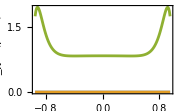
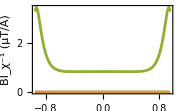
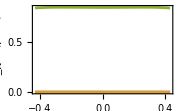

```mathematica
LoopFieldPlot[First[%], {1,-2,2}, 1, 1, ImageSize -> Small]
```

In some cases, it is essential that the coil configurations do not obstruct specific regions, particularly if optical access is required for experimental purposes. Such constraints may be incorporated while optimising the coil parameters. Let us optimise three coils again to generate a uniform field, this time with an axial constraint that the separations must lie between 0.5 and 1 times the coil radius:

```mathematica
FindLoopCoil[{1, -2, 2}, 1, {0.5, 1}]
```

{}

No solutions are found, so we try a different set of turn ratios:

```mathematica
FindLoopCoil[{1, -3, 3}, 1, {0.5, 1}]
```

{{Coilχc[1]→0.500356,Coilχc[2]→0.787322,Coilχc[3]→0.95915,DesToErr→8.71021},{Coilχc[1]→0.501056,Coilχc[2]→0.788102,Coilχc[3]→0.960558,DesToErr→8.67296},{Coilχc[1]→0.501842,Coilχc[2]→0.788971,Coilχc[3]→0.962134,DesToErr→8.63167},{Coilχc[1]→0.502153,Coilχc[2]→0.789315,Coilχc[3]→0.962758,DesToErr→8.61546},{Coilχc[1]→0.503082,Coilχc[2]→0.790335,Coilχc[3]→0.964613,DesToErr→8.56759},{Coilχc[1]→0.503493,Coilχc[2]→0.790784,Coilχc[3]→0.965432,DesToErr→8.54664},{Coilχc[1]→0.503996,Coilχc[2]→0.791331,Coilχc[3]→0.966432,DesToErr→8.52122},{Coilχc[1]→0.50449,Coilχc[2]→0.791867,Coilχc[3]→0.967412,DesToErr→8.49646},{Coilχc[1]→0.504938,Coilχc[2]→0.792351,Coilχc[3]→0.968299,DesToErr→8.47417},{Coilχc[1]→0.505049,Coilχc[2]→0.792471,Coilχc[3]→0.968519,DesToErr→8.46868}}

Inspect the coil plot to see that the axial constraints were respected:

```mathematica
LoopCoilPlot[First[%],{1,-3,-3},1,1,ImageSize->500]
```

## Examples of Saddle and Ellipse Coils

For examples and optimisation involving saddle and ellipse-based coils, please refer to the examples provided in the documentation pages for FindSaddleCoil and FindEllipseCoil.

Related Guides

Creating Coils

Related Tech Notes

## Metadata

### Categorization

Tech Note

NoahH/CreateCoil

NoahH`CreateCoil`

NoahH/CreateCoil/tutorial/PhysicsofCreatingSimpleDiscreteCoils

### Keywords

Loop, Loops, Saddle, Saddles, Arc, Arcs, Ellipse, Ellipses, Coil, Coils, Physics, Magnetism, Electromagnetism, Field, Biot, Savart, Optimization, Optimisation, Optimize, Optimise